## Load MathQ - beta

```mathematica
SetDirectory[NotebookDirectory[]];

nb=CreateDocument[Get["MathQ-beta.nb"], WindowSelected->False];
NotebookEvaluate@nb;
NotebookClose[nb];
```

## Demo 1: SSH model

#### Build a linear chain

Custom lattice (building it “by hand”) : 

	BuildLattice[{BravaisVectors, {“Sublattice1” -> {SitePositions}, “Sublattice2” -> {SitePositions}, ...}}]

```mathematica
latSSH = BuildLattice[{{{2}},{"A"->{{0}},"B"->{{1}}}}]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=1, EmbeddingDimensions=1>]

```mathematica
PlotLattice[latSSH]
```

-Graphics-

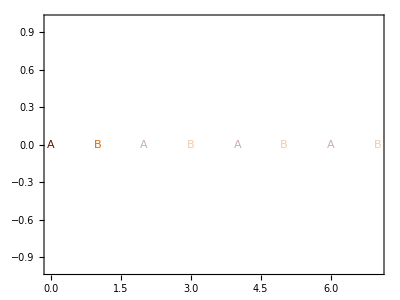

```mathematica
PlotLattice[latSSH,Labels->"Tags", UnitCells->4, Axes->True, Frame->True]
```

#### Implement the SSH model with alternating hoppings

SSH model - implemented by a hopping function

	BuildSystem[lattice, Onsite -> Function[{r}, f[r]], Hopping -> Function[{r1, r2}, g[r1,r2]]

```mathematica
AlternatingHopping[t1_,t2_] = Function[{r1,r2},If[EvenQ[Round[Min[r1[[1]],r2[[1]]]]],t1,t2]];
sysSSH[t1_,t2_] = BuildSystem[latSSH, Hopping->AlternatingHopping[t1,t2]]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=1>]

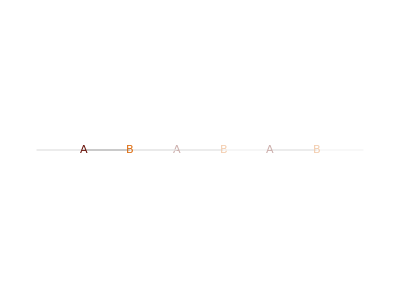

```mathematica
PlotLattice[sysSSH[t1,t2],Labels->"Tags",UnitCells->3,LinkTooltips->True,SiteTooltips->True]
```

#### Bandstructure

Bloch phases
	system[ϕ] gives a system with Bloch phase ϕ = k·a_0

```mathematica
Bands[sysSSH[1,2][ϕ],{ϕ,0,2π}]
```

{{{1.25664×10^-7,-3.},{0.120864,-2.99513},{0.251894,-2.97889},{0.374241,-2.9535},{0.494188,-2.91915},{0.624302,-2.8715},{0.745732,-2.81751},{0.877329,-2.74897},{1.00653,-2.67193},{1.12704,-2.59178},{1.25772,-2.49639},{1.37972,-2.39993},{1.49931,-2.29906},{1.62908,-2.18335},{1.75016,-2.07036},{1.8814,-1.94357},{2.01025,-1.8161},{2.13041,-1.69604},{2.26074,-1.56653},{2.38239,-1.44861},{2.5142,-1.32731},{2.64362,-1.21893},{2.76435,-1.13193},{2.89524,-1.05866},{3.01746,-1.01527},{3.13727,-1.00002},{3.26725,-1.01565},{3.38855,-1.05894},{3.52001,-1.13269},{3.64907,-1.22642},{3.76945,-1.32772},{3.9,-1.44785},{4.02186,-1.56596},{4.14132,-1.6846},{4.27095,-1.81413},{4.3919,-1.93388},{4.52301,-2.06083},{4.64544,-2.17541},{4.76547,-2.28303},{4.89567,-2.39354},{5.01718,-2.49006},{5.14886,-2.58669},{5.27814,-2.67286},{5.39874,-2.74497},{5.5295,-2.81366},{5.65158,-2.8685},{5.77126,-2.91328},{5.9011,-2.95154},{6.02227,-2.97735},{6.1536,-2.9944},{6.28319,-3.}},{{1.25664×10^-7,3.},{0.120864,2.99513},{0.251894,2.97889},{0.374241,2.9535},{0.494188,2.91915},{0.624302,2.8715},{0.745732,2.81751},{0.877329,2.74897},{1.00653,2.67193},{1.12704,2.59178},{1.25772,2.49639},{1.37972,2.39993},{1.49931,2.29906},{1.62908,2.18335},{1.75016,2.07036},{1.8814,1.94357},{2.01025,1.8161},{2.13041,1.69604},{2.26074,1.56653},{2.38239,1.44861},{2.5142,1.32731},{2.64362,1.21893},{2.76435,1.13193},{2.89524,1.05866},{3.01746,1.01527},{3.13727,1.00002},{3.26725,1.01565},{3.38855,1.05894},{3.52001,1.13269},{3.64907,1.22642},{3.76945,1.32772},{3.9,1.44785},{4.02186,1.56596},{4.14132,1.6846},{4.27095,1.81413},{4.3919,1.93388},{4.52301,2.06083},{4.64544,2.17541},{4.76547,2.28303},{4.89567,2.39354},{5.01718,2.49006},{5.14886,2.58669},{5.27814,2.67286},{5.39874,2.74497},{5.5295,2.81366},{5.65158,2.8685},{5.77126,2.91328},{5.9011,2.95154},{6.02227,2.97735},{6.1536,2.9944},{6.28319,3.}}}

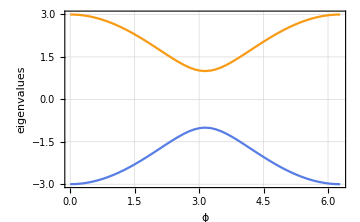

```mathematica
PlotBands[Bands[sysSSH[1,2][ϕ],{ϕ,0,2π}], FrameLabel->{"ϕ","eigenvalues"}]
```

```mathematica
Manipulate[
PlotBands[Bands[sysSSH[t1,t2][kx],{kx,0,2π}], FrameLabel->{"ϕ","eigenvalues"},PlotRange->{-3,3}],
{{t1,1},0,2},{t2,0,2}]
```

#### Finite length SSH chain

We build a finite length lattice. This time we use a lattice preset (“linear”)

```mathematica
LatticePresets
```

{BCC,Cubic,FCC,Honeycomb,Linear,Square,Triangular,TwistedHoneycombBilayer,TwistedHoneycombBilayer,HoneycombNanoribbon}

```mathematica
latSSHfinite=BuildLattice["Linear",Bounded->{Region->Function[{r},0≤r[[1]]<99]}]
```

MQLattice[<NumberOfSites=99, LatticeDimensions=0, EmbeddingDimensions=1>]

```mathematica
sysSSHfinite[t1_,t2_]=BuildSystem[latSSHfinite, Hopping->AlternatingHopping[t1,t2]]
```

MQSystem[<NumberOfSites=99, SiteDimensions=1, LatticeDimensions=0>]

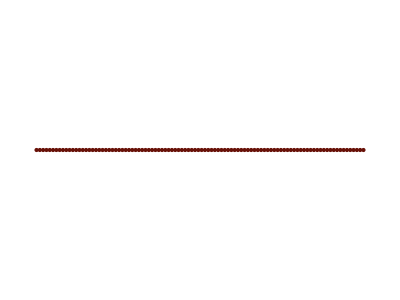

```mathematica
PlotLattice[sysSSHfinite[t1,t2], LinkTooltips->True]
```

```mathematica
sysSSHfinite[Subscript[t, 1],Subscript[t, 2]]["H"]
MatrixForm[%[[1;;10,1;;10]]]
```

SparseArray[<198>, {100, 100}]

(0 | t_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t_1 | 0 | t_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t_2 | 0 | t_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t_1 | 0 | t_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t_2 | 0 | t_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t_1 | 0 | t_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t_2 | 0 | t_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t_1 | 0 | t_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t_2 | 0 | t_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t_1 | 0)

Density of states

{-1.49934,-1.49737,-1.49408,-1.48949,-1.4836,-1.47641,-1.46793,-1.45819,-1.44718,-1.43493,-1.42145,-1.40676,-1.39088,-1.37384,-1.35565,-1.33635,-1.31596,-1.29452,-1.27206,-1.24861,-1.22421,-1.19891,-1.17275,-1.14577,-1.11803,-1.08959,-1.0605,-1.03083,-1.00065,-0.970043,-0.939082,-0.907866,-0.876497,-0.845088,-0.813766,-0.782672,-0.751966,-0.721825,-0.69245,-0.664066,-0.636924,-0.611305,-0.587514,-0.565883,-0.546757,-0.530487,-0.51741,-0.507824,-0.501969,0,0.501969,0.507824,0.51741,0.530487,0.546757,0.565883,0.587514,0.611305,0.636924,0.664066,0.69245,0.721825,0.751966,0.782672,0.813766,0.845088,0.876497,0.907866,0.939082,0.970043,1.00065,1.03083,1.0605,1.08959,1.11803,1.14577,1.17275,1.19891,1.22421,1.24861,1.27206,1.29452,1.31596,1.33635,1.35565,1.37384,1.39088,1.40676,1.42145,1.43493,1.44718,1.45819,1.46793,1.47641,1.4836,1.48949,1.49408,1.49737,1.49934}

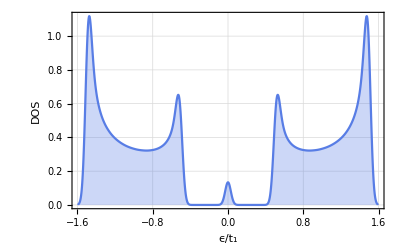

```mathematica
Spectrum[sysSSHfinite[1.0,0.5]]
SmoothHistogram[%,.03, Filling->Axis, FrameLabel->{"ϵ/t_1","DOS"}, PlotDefaults]
```

{-2.99868,-2.99474,-2.98817,-2.97898,-2.96719,-2.95281,-2.93587,-2.91637,-2.89436,-2.86986,-2.8429,-2.81352,-2.78176,-2.74767,-2.7113,-2.6727,-2.63192,-2.58904,-2.54411,-2.49721,-2.44842,-2.39782,-2.34549,-2.29154,-2.23607,-2.17918,-2.12101,-2.06167,-2.00131,-1.94009,-1.87816,-1.81573,-1.75299,-1.69018,-1.62753,-1.56534,-1.50393,-1.44365,-1.3849,-1.32813,-1.27385,-1.22261,-1.17503,-1.13177,-1.09351,-1.06097,-1.03482,-1.01565,-1.00394,0,1.00394,1.01565,1.03482,1.06097,1.09351,1.13177,1.17503,1.22261,1.27385,1.32813,1.3849,1.44365,1.50393,1.56534,1.62753,1.69018,1.75299,1.81573,1.87816,1.94009,2.00131,2.06167,2.12101,2.17918,2.23607,2.29154,2.34549,2.39782,2.44842,2.49721,2.54411,2.58904,2.63192,2.6727,2.7113,2.74767,2.78176,2.81352,2.8429,2.86986,2.89436,2.91637,2.93587,2.95281,2.96719,2.97898,2.98817,2.99474,2.99868}

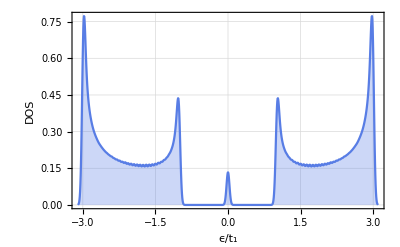

```mathematica
Spectrum[sysSSHfinite[1.0,2.0]]
SmoothHistogram[%,.03, Filling->Axis, FrameLabel->{"ϵ/t_1","DOS"}, PlotDefaults]
```

Wavefunctions

```mathematica
Eigenstates[sysSSHfinite[1.0,1.5],Levels->1]
```

{{{-0.527046},{-6.88793×10^-10},{0.351364},{1.49248×10^-9},{-0.234243},{-2.54481×10^-9},{0.156162},{4.02133×10^-9},{-0.104108},{-6.16803×10^-9},{0.0694053},{9.34274×10^-9},{-0.0462702},{-1.40746×10^-8},{0.0308468},{2.11521×10^-8},{-0.0205645},{-3.17551×10^-8},{0.0137097},{4.76505×10^-8},{-0.00913979},{-7.14877×10^-8},{0.00609319},{1.0724×10^-7},{-0.00406213},{-1.60865×10^-7},{0.00270809},{2.41301×10^-7},{-0.00180539},{-3.61953×10^-7},{0.00120359},{5.42931×10^-7},{-0.000802396},{-8.14398×10^-7},{0.00053493},{1.2216×10^-6},{-0.00035662},{-1.8324×10^-6},{0.000237747},{2.7486×10^-6},{-0.000158498},{-4.12289×10^-6},{0.000105665},{6.18434×10^-6},{-0.0000704435},{-9.27651×10^-6},{0.0000469623},{0.0000139148},{-0.0000313082},{-0.0000208722},{0.0000208722},{0.0000313082},{-0.0000139148},{-0.0000469623},{9.27651×10^-6},{0.0000704435},{-6.18434×10^-6},{-0.000105665},{4.12289×10^-6},{0.000158498},{-2.7486×10^-6},{-0.000237747},{1.8324×10^-6},{0.00035662},{-1.2216×10^-6},{-0.00053493},{8.14398×10^-7},{0.000802396},{-5.42931×10^-7},{-0.00120359},{3.61953×10^-7},{0.00180539},{-2.41301×10^-7},{-0.00270809},{1.60865×10^-7},{0.00406213},{-1.0724×10^-7},{-0.00609319},{7.14878×10^-8},{0.00913979},{-4.76505×10^-8},{-0.0137097},{3.17551×10^-8},{0.0205645},{-2.11521×10^-8},{-0.0308468},{1.40745×10^-8},{0.0462702},{-9.34275×10^-9},{-0.0694053},{6.16799×10^-9},{0.104108},{-4.02129×10^-9},{-0.156162},{2.54483×10^-9},{0.234243},{-1.49244×10^-9},{-0.351364},{6.888×10^-10},{0.527046}}}

{-0.506377,-1.30694×10^-9,1.30694×10^-9}

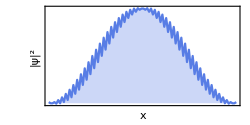
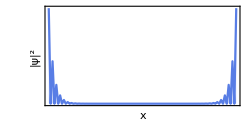
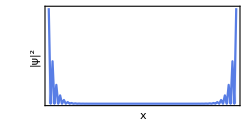

```mathematica
PlotEigenstates[sysSSHfinite[1.0,1.5],Levels->3, 
Filling->Axis, FrameLabel->{"x","|ψ|^2"}, PlotRange->All,PrintEigenvalues->True,PlotDefaults]
```

## Demo 2: Kitaev model

#### Infinite Kitaev wire

Kitaev model: H=∑_⟨i,j⟩ -w c_i^+c_j± Δc_i^+c_j^+∓s Δ c_i c_j, where ±=sign(x_i-x_j)

We can express it as H -μ N =1/2 [∑_⟨i,j⟩ (c_i^+,c_j)·(-w | ± Δ
∓ Δ | w)·(c_i
c_j^+)  + ∑_i (c_i^+,c_i)·(-μ | 0
0 | μ)·(c_i
c_i^+)]  (Bogoliubov - Nambu notation)

```mathematica
latLinear=BuildLattice["Linear"]

KitaevOnsite = Function[{r},({{-μ, 0}, {0, μ}}) ];
KitaevHopping = Function[{r1,r2},({{-w, 0}, {0, w}})+Sign[(r1-r2)[[1]]]({{0, Δ}, {-Δ, 0}}) ]

sysKitaev[w_,Δ_,μ_] = BuildSystem[latLinear,Onsite->KitaevOnsite,Hopping->KitaevHopping, Nambu->True]
```

MQLattice[<NumberOfSites=1, LatticeDimensions=1, EmbeddingDimensions=1>]

Function[{r1,r2},{{-w,0},{0,w}}+Sign[(r1-r2)⟦1⟧] {{0,Δ},{-Δ,0}}]

MQSystem[<NumberOfSites=1, SiteDimensions=2, LatticeDimensions=1>]

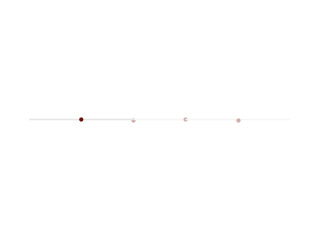

```mathematica
PlotLattice[sysKitaev[w,Δ,μ],UnitCells->4]
```

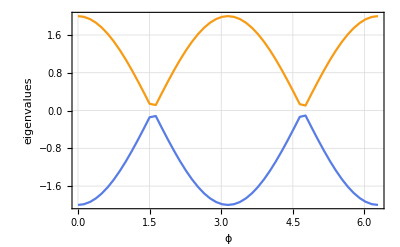

```mathematica
PlotBands[Bands[sysKitaev[1,0,0][ϕ],{ϕ,0,2π}],FrameLabel->{"ϕ","eigenvalues"}]
```

Is that an anticrossing?

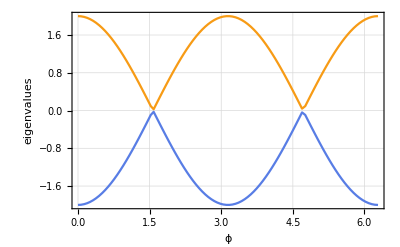

```mathematica
PlotBands[Bands[sysKitaev[1,0,0][ϕ],{ϕ,0,2π},SamplePoints->100], FrameLabel->{"ϕ","eigenvalues"}]
```

Advanced interpolating sampling: UntangledBands

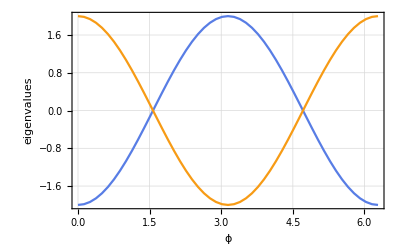

```mathematica
PlotBands[UntangledBands[sysKitaev[1,0,0][ϕ],{ϕ,0,2π}], FrameLabel->{"ϕ","eigenvalues"}]
```

Topological transition at |μ|=2|w|

```mathematica
Manipulate[
PlotBands[UntangledBands[sysKitaev[w,Δ,μ][ϕ],{ϕ,0,2π}], 
FrameLabel->{"ϕ","eigenvalues"},
PlotRange->{-5,5}, PlotLabel->"μ/w = "~~ToString[μ/w]],
{{w,1},0,1},{Δ,0,1},{{μ,0},-4,4}]
```

BDI-class topological invariant: ν=sign∏_k Pf[τ_x H_k]
(A general Pfafian implementation by M. Wimmer can be found in https://arxiv.org/src/1102.3440v2/anc/pfapack/mathematica/pfaffian.nb)

```mathematica
invariant[w_,Δ_,μ_]:=Sign[Pfaffian[({{0, 1}, {1, 0}}).sysKitaev[w,Δ,μ][0]["Flat"]["H"]]*Pfaffian[({{0, 1}, {1, 0}}).sysKitaev[w,Δ,μ][π]["Flat"]["H"]]]
Manipulate[
PlotBands[
UntangledBands[sysKitaev[w,Δ,μ][ϕ],{ϕ,0,2π}], 
FrameLabel->{"ϕ","eigenvalues"},
PlotLabel->"invariant = "~~ToString[invariant[w,Δ,μ]],
PlotRange->{-5,5}],
{{w,1},0,1},{Δ,0,1},{{μ,0},-3,3}]
```

#### Finite length Kitaev chain

```mathematica
latLinearFinite=BuildLattice["Linear",Bounded->{Region->Function[{r},0≤r[[1]]<100]}]
sysKitaevFinite[w_,Δ_,μ_]=BuildSystem[latLinearFinite,Onsite->KitaevOnsite,Hopping->KitaevHopping, Nambu->True]
```

MQLattice[<NumberOfSites=100, LatticeDimensions=0, EmbeddingDimensions=1>]

MQSystem[<NumberOfSites=100, SiteDimensions=2, LatticeDimensions=0>]

Density of states

Non-topological: |μ| > 2|w|

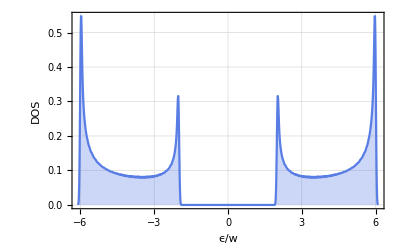

```mathematica
Spectrum[sysKitaevFinite[1.0,1.0, 4.0]];
SmoothHistogram[%,.03, Filling->Axis, FrameLabel->{"ϵ/w","DOS"},PlotRange->All, PlotDefaults]
```

Topological: |μ| < 2|w|

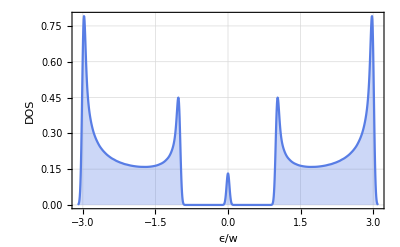

```mathematica
Spectrum[sysKitaevFinite[1.0,1, 1]];
SmoothHistogram[%,.03, Filling->Axis, FrameLabel->{"ϵ/w","DOS"}, PlotRange->All,PlotDefaults]
```

Majoranas at the edges

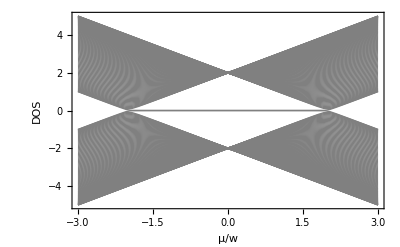

```mathematica
PlotBands[Bands[sysKitaevFinite[1.0,1, μ], {μ,-3,3}],FrameLabel->{"μ/w","DOS"}, PlotStyle->Directive[{Thin,Gray}], GridLines->None]
```

{4.77049×10^-17,5.20416×10^-17}

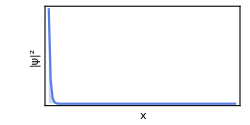
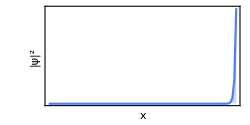

```mathematica
PlotEigenstates[sysKitaevFinite[1.0,1, 1],Levels->2, Filling->Axis, FrameLabel->{"x","|ψ|^2"}, PlotRange->All,PrintEigenvalues->True,PlotDefaults]
```

## Demo 3: Haldane model

#### Build a honeycomb lattice

```mathematica
latHoneycomb=BuildLattice["Honeycomb"]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

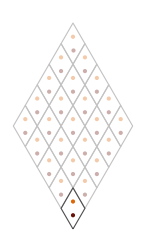

```mathematica
PlotLattice[latHoneycomb, UnitCells->5]
```

#### Build a graphene monolayer system (nearest neighbor)

```mathematica
sysgraphene=BuildSystem[latHoneycomb, HoppingRange->1/√3, Onsite->Function[{r},0], Hopping->Function[{r1,r2},-3.16]]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=2>]

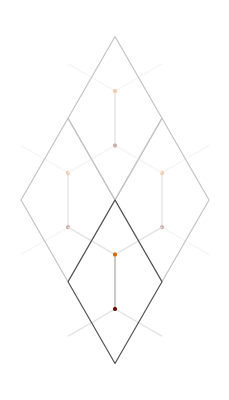

```mathematica
PlotLattice[sysgraphene, LinkTooltips->True, SiteTooltips->True]
```

#### Plot bandstructure

Passing multiple Bloch phases and wave-vectors:
	system[{ϕ1,ϕ2,...}]
	system[A·{k1,k2,...}], where A = lattice[“BravaisVectors”] is the Bravais matrix

```mathematica
A = latHoneycomb["BravaisVectors"]
PlotBands[Bands[sysgraphene[A.{kx,ky}],{kx,-2π,2π},{ky,-2π,2π}, SamplePoints->91],BoxRatios->{1,1,1}]
```

{{0.5,0.866025},{-0.5,0.866025}}

-Graphics3D-

#### Haldane model

Haldane model: graphene + alternating imaginary next-nearest neighbor hopping

```mathematica
Haldane=With[{t2=0.3, t=3.16},Function[{r1,r2,tag1,tag2},If[Norm[r1-r2]≤1/√3,t,ⅈ t2 Cos[3ArcTan@@(r1-r2)]If[tag1==="A",1,-1]]]];
sysHaldane=BuildSystem[latHoneycomb, HoppingRange->1,Hopping->Haldane]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=2>]

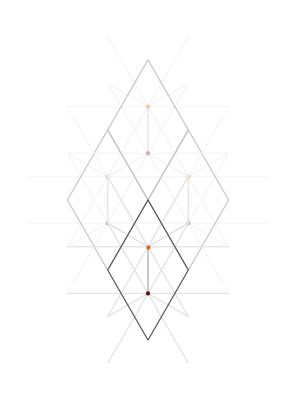

```mathematica
PlotLattice[sysHaldane, LinkTooltips->True, SiteTooltips->True]
```

```mathematica
PlotBands[Bands[sysHaldane[A.{kx,ky}],{kx,-2π,2π},{ky,-2π,2π}, SamplePoints->91], BoxRatios->{1,1,1}]
```

-Graphics3D-

#### Berry curvature

Algorithm: T. Fukui and Y. Hatsugai and H. Suzuki - J. Phys. Soc. Jpn.  74  1674-1677  (2005)

```mathematica
berrymesh=BerryMesh[sysHaldane,SamplePoints->50];
```

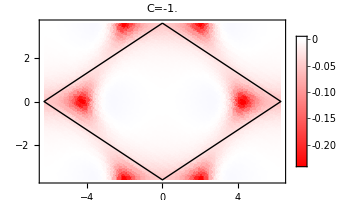
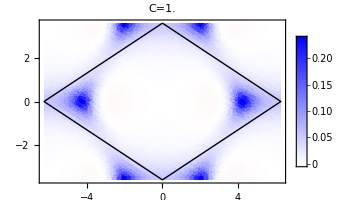

```mathematica
PlotBerryMesh[latHoneycomb, berrymesh, PlotLegends->Automatic, ImageSize->300]
```

#### Nanoribbon geometry

Build a generic nanoribbon, apply the Haldane model

MQLattice[<NumberOfSites=250, LatticeDimensions=1, EmbeddingDimensions=2>]

MQSystem[<NumberOfSites=250, SiteDimensions=1, LatticeDimensions=1>]

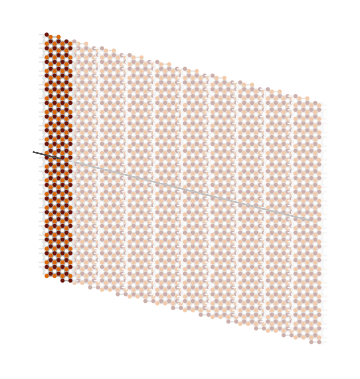

```mathematica
W=30; ChiralIntegers={3,-4}; RibbonAxis=Normalize[({{Cos[π/3], Cos[2π/3]}, {Sin[π/3], Sin[2π/3]}}).ChiralIntegers];

latRibbon=BuildLattice["Honeycomb", Supercell->{ChiralIntegers,{1,1}},Bounded->{Axes->{2},Region->(-W/2<=#.({{0, -1}, {1, 0}}).RibbonAxis<=W/2&)}]
sysHaldaneRibbon=BuildSystem[latRibbon, HoppingRange->1,Hopping->Haldane]

PlotLattice[sysHaldaneRibbon, UnitCells->10, ImageSize->Medium, PlotDirectives->PointSize[Medium]]
```

#### Nanoribbon bands

```mathematica
latRibbon["BravaisVectors"]
```

{{1.,0.}}

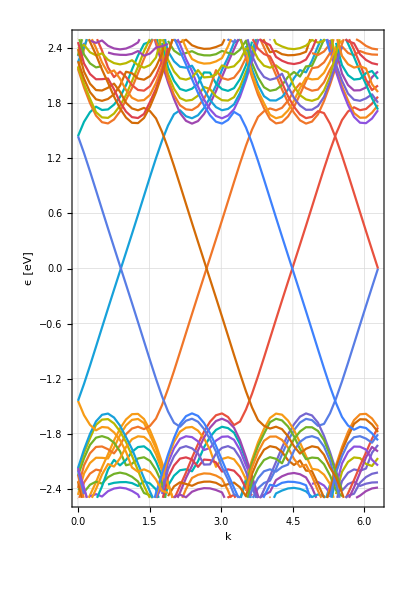

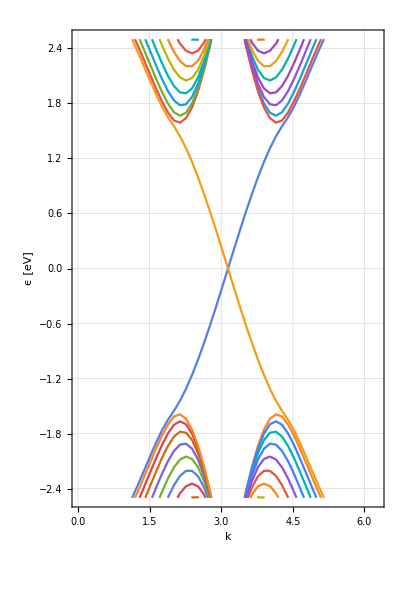

```mathematica
PlotBands[UntangledBands[sysHaldaneRibbon[latRibbon["BravaisVectors"].{k, 0}],{k,0,2π},Levels->32], FrameLabel->{"k","ϵ [eV]"}, PlotRange->{-2.5,2.5}, AspectRatio->1.5]
```

We can color the bands depending on eigenstate properties: which side of the ribbon is each state at?

```mathematica
uppersites= Flatten[Position[latRibbon["FlatSites"],{x_,y_}/;y>0]];
upperhalf= Function[{vec},Norm[Flatten[vec[[uppersites]]]]];
```

```mathematica
PlotBands[UntangledBands[sysHaldaneRibbon[k],{k,0,2π},Levels->32, EigenstateObservable->upperhalf], 
FrameLabel->{"kA","ϵ [eV]"}, PlotRange->{{0,2π},{-2.5,2.5}}, AspectRatio->1.5, 
ObservableToStyle->Function[{z},Blend[{{0,Red},{1,Lighter[Gray]}},z]]]
```

-Graphics-

## Demo 4: Kane-Mele graphene nanoribbon

#### The Kane-Mele model

Kane-Mele model: graphene with an opposite Haldane term for each spin sector

```mathematica
KaneMele=With[{t2=0.1,t=3.16},Function[{r1,r2,tag1,tag2},If[Norm[r1-r2]≤1/√3,t({{1, 0}, {0, 1}}),ⅈ t2({{1, 0}, {0, -1}})Cos[3ArcTan@@(r1-r2)[[1;;2]]]If[tag1==="A",1,-1]]]];
sysKaneMele=BuildSystem[latHoneycomb,HoppingRange->1,Onsite->Function[{r},({{0, 0}, {0, 0}})],Hopping->KaneMele]
```

MQSystem[<NumberOfSites=2, SiteDimensions=2, LatticeDimensions=2>]

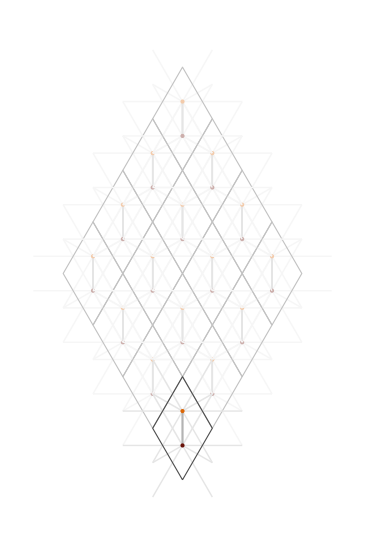

```mathematica
PlotLattice[sysKaneMele, SiteTooltips->True, LinkTooltips->True, SiteRadius->0.2, LinkRadius->0.05,BoxCenterAtOrigin->True, UnitCells->4]
```

Kane-Mele nanoribbon

MQSystem[<NumberOfSites=250, SiteDimensions=2, LatticeDimensions=1>]

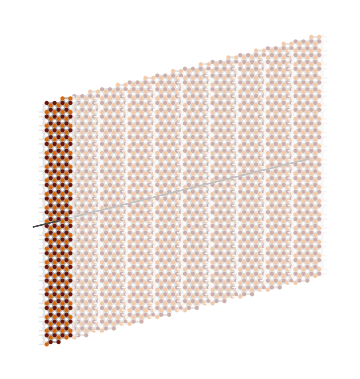

```mathematica
sysKaneMeleRibbon[Zeeman_] = BuildSystem[latRibbon, HoppingRange->1,Onsite->Function[{r},Zeeman({{1, 0}, {0, -1}})],Hopping->KaneMele]

PlotLattice[sysKaneMeleRibbon[0], UnitCells->10, ImageSize->Medium, PlotDirectives->PointSize[Medium]]
```

#### Bands

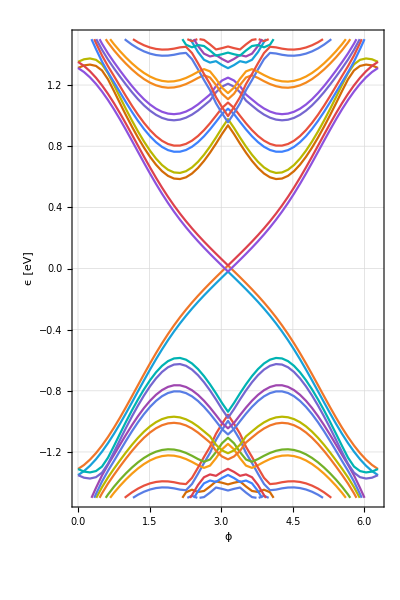

```mathematica
PlotBands[UntangledBands[sysKaneMeleRibbon[0.02][ϕ],{ϕ,0,2π},Levels->32], FrameLabel->{"ϕ","ϵ [eV]"}, PlotRange->{-1.5,1.5}, AspectRatio->1.5]
```

Quantum Spin-Hall: counter-propagating spins

```mathematica
PlotBands[UntangledBands[sysKaneMeleRibbon[0.05][k],{k,0,2π},Levels->32, EigenstateObservable->upperhalf], 
FrameLabel->{"kA","ϵ [eV]"}, PlotRange->{{0,2π},{-1.5,1.5}}, AspectRatio->1.5, 
ObservableToStyle->Function[{z},Blend[{{0,Red},{1,Lighter[Gray]}},z]]]
```

-Graphics-

```mathematica
spin=Function[{vec},Total[#*.({{1, 0}, {0, -1}}).#&/@vec]];
```

```mathematica
PlotBands[UntangledBands[sysKaneMeleRibbon[0.05][k],{k,0,2π},Levels->32, EigenstateObservable->spin], 
FrameLabel->{"kA","ϵ [eV]"}, PlotRange->{{0,2π},{-1.5,1.5}}, AspectRatio->1.5, 
ObservableToStyle->Function[{z},Blend[{{-1,Red},{1,Blue}},z]]]
```

-Graphics-

#### Edge modes

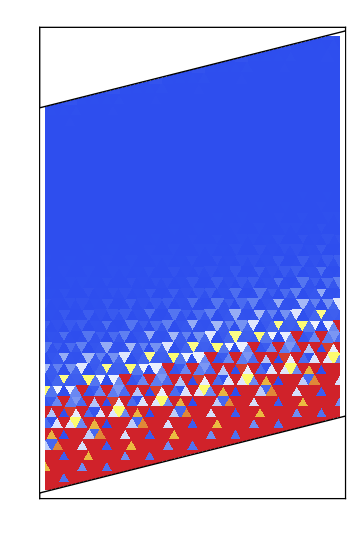
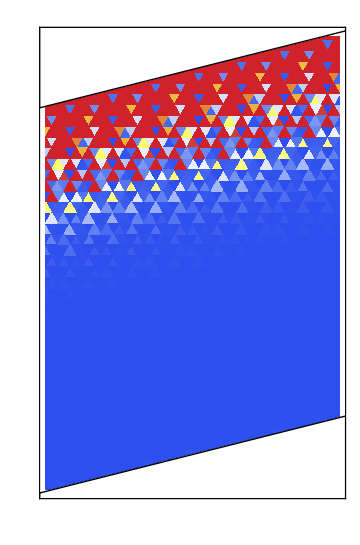

```mathematica
With[{ϕ=0.99π},PlotEigenstates[latRibbon,sysRibbon[ϕ],
Levels->2,
UnitCells->7,
ImageSize->Medium,
MaskRegion->(-W/2<=#.({{0, -1}, {1, 0}}).RibbonAxis<=W/2&)]]
```

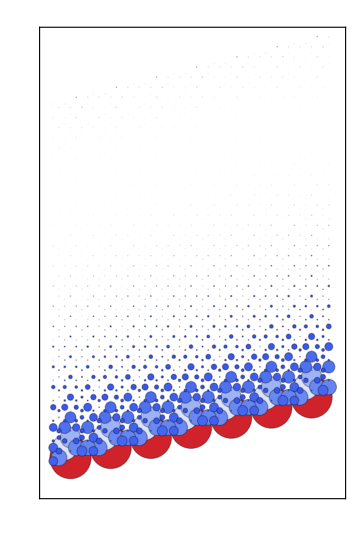
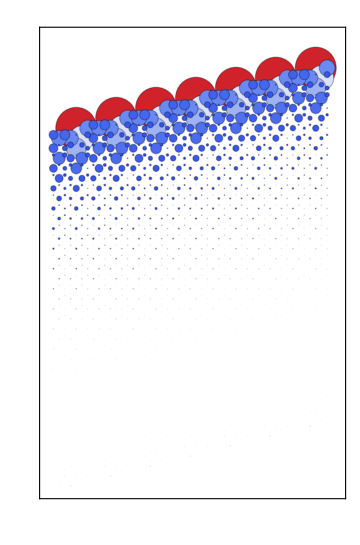

```mathematica
With[{z=0.51},PlotEigenstates[latRibbon,sysRibbon[2π z],
Levels->2,
UnitCells->7,
ImageSize->Medium,
BubblePlot->True]]
```